## Chapter 1

### Phase diagram Lifshitz

{{0,1},{0,1}}

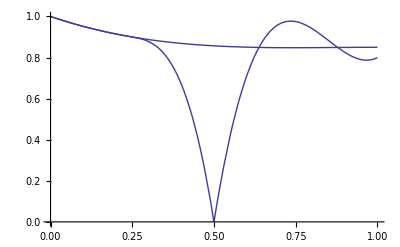

```mathematica
range={{0,1},{0,1}}

ptsFerroPara={{{0},1},{{1/4},0.9},{{1},0.85,0}};
lineFerroPara=Interpolation[ptsFerroPara];
(* make sure the 2 lines are tangent when they split *)
deriv=D[lineFerroPara[x],x]/.x->1/4;
ptsFerroMod={{{1/4},0.9,deriv},{{1/2},0,-10}};
lineFerroMod=If[x<1/4,lineFerroPara,Interpolation[ptsFerroMod]];
ptsModAnti={{{1/2},0,+10},{{1},0.8,0.8}};
lineModAnti=If[x<1/2,2,Interpolation[ptsModAnti]];
pFerroPara=Plot[lineFerroPara[x],{x,0,1},PlotRange->range];
pFerroMod=Plot[lineFerroMod[x],{x,0,1},PlotRange->range];
pModAnti=Plot[lineModAnti[x],{x,0,1},PlotRange->range];
Show[pFerroMod,pFerroPara,pModAnti]
```

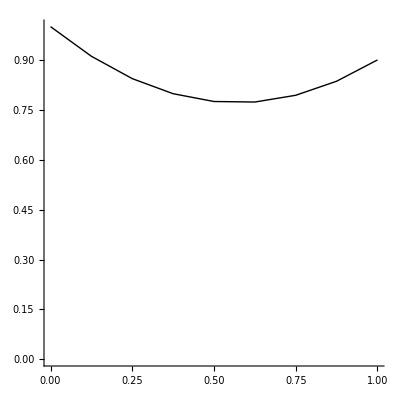

```mathematica
lineFerroPara=BezierCurve[{{0,1},{0.5,0.6},{1,0.9}}];
lineFerroMod=BezierCurve[{{
Graphics[{lineFerroPara},PlotRange->range,Axes->True]
```